```mathematica
Phi[x_,xI_,dx_]=Piecewise[{{1-RealAbs[x-xI]/dx, RealAbs[x-xI]≤dx}, {0, true}}]
```

Piecewise[{{1-RealAbs[x-xI]/dx, RealAbs[x-xI]≤dx}, {0, True}}]

```mathematica
Plot3D[Phi[0,xI,1]Phi[0,yI,1],{xI,-2,2},{yI,-2,2},PlotRange->Full]
```

-Graphics3D-

```mathematica
Grad[Phi[x,xI,h]Phi[y,yI,h],{xI,yI}]
Grad[Phi[0,xI,1]Phi[0,yI,1],{xI,yI}]/.{xI->.5,yI->.2}
```

{(Piecewise[{{1-RealAbs[y-yI]/h, RealAbs[y-yI]≤h}, {0, True}}]) (Piecewise[{{1/h, x-xI≥0&&h-x+xI≥0}, {-1/h, (x-xI≥0&&h-x+xI≥0)||(x-xI<0&&h+x-xI≥0)}, {0, True}}]),(Piecewise[{{1-RealAbs[x-xI]/h, RealAbs[x-xI]≤h}, {0, True}}]) (Piecewise[{{1/h, y-yI≥0&&h-y+yI≥0}, {-1/h, (y-yI≥0&&h-y+yI≥0)||(y-yI<0&&h+y-yI≥0)}, {0, True}}])}

{-0.8,-0.5}

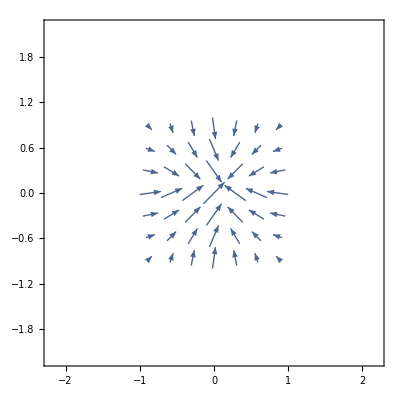

```mathematica
VectorPlot[Grad[Phi[0,xI,1]Phi[0,yI,1],{xI,yI}]/.{xI->x,yI->y},{x,-2,2},{y,-2,2},PlotRange->Full]
```